```mathematica
NS["monte_carlo_tests"]
```

```mathematica
setdirectory
```

C:\Users\pglpm\repositories\genobayes\scripts2

```mathematica
<<"mcmc.m"
```

```mathematica
ev[a_]:=Mean[BetaDistribution[Sequence@@Reverse[a]]];
sd[a_]:=Sqrt@Variance[BetaDistribution[Sequence@@Reverse[a]]];
```

```mathematica
cbd[a_,b_]:=Table[{RandomVariate[BetaDistribution[Sequence@@a]],RandomVariate[BetaDistribution[Sequence@@b]]},1];
```

```mathematica
data=Import["dataset1_binarized.csv"][[2;;,2;;]];
```

```mathematica
symptoms={{1}};
snps={3+{6}};
symptomvariants={{0},{1}};
snpvariants={{0},{1}};
(*snpvariants={{0,0},{0,1},{1,0},{1,1}};*)
namesymptomvariants={"n","y"};
namesymptoms="";
```

```mathematica
numsymptoms=Length[symptoms];numsymptomvariants=Length[symptomvariants];numsnps=Length[snps];numsnpvariants=Length[snpvariants];namestatistics=Flatten@Table[ii<>jj,{ii,{"EV_","SD_","post.theta_","opt.theta_","max.spread_"}},{jj,namesymptomvariants}];
```

```mathematica
thetas={t1,t2}
```

{t1,t2}

```mathematica
sdata=data[[;;,Join[symptoms[[1]],snps[[1]]]]];
```

```mathematica
(f=Table[Total[Boole/@Table[z==Join[symptomvariant,snpvariant],{z,sdata}]],{symptomvariant,symptomvariants},{snpvariant,snpvariants}])//MF
```

(1481 | 2887
502 | 1159)

```mathematica
ClearAll[cd,gd];
gd[x_]=Assuming[x>0,FS[PDF[GammaDistribution[1,1000],x]]];

gd2[x_]=Assuming[x>0,FS[PDF[GammaDistribution[1/1000^2,1000^2],x]]];


cd[x_]=Assuming[x>0,FS@Log[PDF[CauchyDistribution[Log[1000],Log[1000]],Log[x]]]];

cd2[x_]=Assuming[x>0,FS@Log[PDF[CauchyDistribution[0,Log[1000]],Log[x]]]];
```

```mathematica
ClearAll[logpriorthetag];logpriorthetag[t_]:=(Log@gd[Total@t]-Log[Total@t]);

ClearAll[logpriorthetag2];logpriorthetag2[t_]:=(Log@gd2[Total@t]-Log[Total@t]);
```

```mathematica
ClearAll[logpriorthetac];logpriorthetac[t_]:=(Total@cd[t]-Total@Log[t]);

ClearAll[logpriorthetac2];logpriorthetac2[t_]:=(Total@cd2[t]-Total@Log[t]);
```

```mathematica
ClearAll[logpriorthetaca];logpriorthetaca[t_]:=(cd2[Total@t]-2*Log[Total@t]);
```

```mathematica
logprobi=Simplify@Block[{r2=f+Exp@thetas},logpriorthetaca[Exp@thetas]+Total@thetas]
```

t1+t2-2 Log[ⅇ^t1+ⅇ^t2]+Log[Log[1000]/(9 π Log[10]^2+π Log[ⅇ^t1+ⅇ^t2]^2)]

```mathematica
mcmc=MCMC[logprobi,{{t1,0,1,Reals},{t2,0,1,Reals}},10000]
```

MCMCResult[{t1→0.357281,t2→0.355406},«10000»]

```mathematica
mcmc=MCMC[logprobi,mcmc,100000]
```

MCMCResult[{t1→-0.860747,t2→-0.840853},«109999»]

```mathematica
{Max@#,Min@#}&@Flatten[mcmc["ParameterRun"][[10000;;]]]
```

{45.0964,-43.951}

```mathematica
mpari=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
ssamples=Cases[samplesi[[;;;;Round[Length[samplesi]/100000]]],{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[ssamples]
```

72227

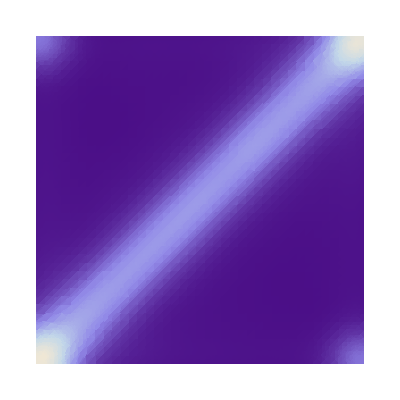

```mathematica
SmoothDensityHistogram[ssamples,"Oversmooth","PDF",ColorFunction->Auto,Mesh->10,MeshStyle->Directive[green,Dashed],PlotRange->{{0,1},{0,1}}]
```

```mathematica
logprobi=Simplify@Block[{r2=f+Exp@thetas},logpriorthetac2[Exp@thetas]+Total@thetas]
```

t1+t2-Log[ⅇ^t1]-Log[ⅇ^t2]-2 Log[π]+2 Log[Log[1000]]+Log[1/(9 Log[10]^2+Log[ⅇ^t1]^2)]+Log[1/(9 Log[10]^2+Log[ⅇ^t2]^2)]

```mathematica
mcmc=MCMC[logprobi,{{t1,0,1,Reals},{t2,0,1,Reals}},10000]
```

MCMCResult[{t1→-12.2325,t2→22.4911},«10000»]

```mathematica
mcmc=MCMC[logprobi,mcmc,100000]
```

MCMCResult[{t1→-7.39848,t2→-0.815794},«109999»]

```mathematica
{Max@#,Min@#}&@Flatten[mcmc["ParameterRun"][[10000;;]]]
```

{84.9642,-159.088}

```mathematica
mpari=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
ssamples=Cases[samplesi[[;;;;Round[Length[samplesi]/100000]]],{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[ssamples]
```

79172

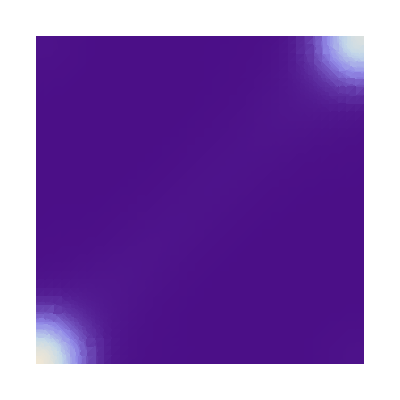

```mathematica
SmoothDensityHistogram[ssamples,"Oversmooth","PDF",ColorFunction->Auto,Mesh->10,MeshStyle->Directive[green,Dashed],PlotRange->{{0,1},{0,1}}]
```

```mathematica
logprobi=Assuming[Element[t1,Reals]&&Element[t2,Reals],FullSimplify@Block[{r2=f+Exp@thetas},logpriorthetac[Exp@thetas]+Total@thetas]]
```

-Log[(t1^2-6 t1 Log[10]+18 Log[10]^2) (t2^2-6 t2 Log[10]+18 Log[10]^2)]+Log[Log[1000]^2/π^2]

```mathematica
mcmc=MCMC[logprobi,{{t1,0,1,Reals},{t2,0,1,Reals}},10000]
```

MCMCResult[{t1→9.25196,t2→9.68673},«10000»]

```mathematica
mcmc=MCMC[logprobi,mcmc,100000]
```

MCMCResult[{t1→5.54301,t2→74.5548},«109999»]

```mathematica
{Max@#,Min@#}&@Flatten[mcmc["ParameterRun"][[10000;;]]]
```

{343.97,-79.553}

```mathematica
mpari=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
ssamples=Cases[samplesi[[;;;;Round[Length[samplesi]/100000]]],{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[ssamples]
```

96637

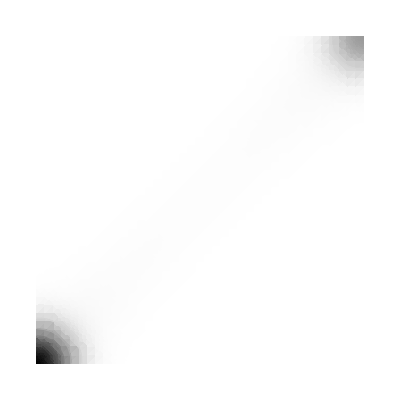

```mathematica
SmoothDensityHistogram[ssamples,"Oversmooth","PDF",ColorFunctionScaling->True,ColorFunction->(GrayLevel[1-#]&),Mesh->5,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

```mathematica
logprobi=Assuming[Element[t1,Reals]&&Element[t2,Reals],FullSimplify@Block[{r2=f+Exp@thetas},logpriorthetag2[Exp@thetas]+Total@thetas]]
```

(-ⅇ^t1-ⅇ^t2)/1000000+t1+t2-(3 Log[10])/500000+Log[1/((ⅇ^t1+ⅇ^t2)^(1999999/1000000) Gamma[1/1000000])]

```mathematica
mcmc=MCMC[logprobi,{{t1,0,1,Reals},{t2,0,1,Reals}},10000]
```

MCMCResult[{t1→-54.7429,t2→-54.7657},«10000»]

```mathematica
mcmc=MCMC[logprobi,mcmc,100000]
```

MCMCResult[{t1→-34.5008,t2→-34.5034},«109999»]

```mathematica
{Max@#,Min@#}&@Flatten[mcmc["ParameterRun"][[10000;;]]]
```

{14.9132,-145.998}

```mathematica
mpari=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
ssamples=Cases[samplesi[[;;;;Round[Length[samplesi]/100000]]],{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[ssamples]
```

31148

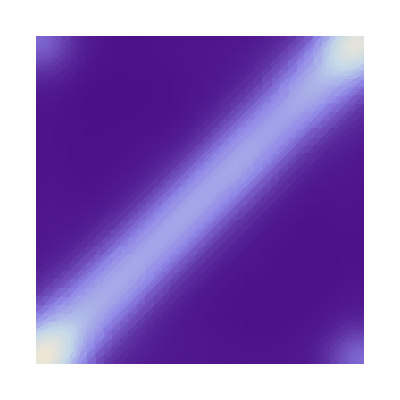

```mathematica
SmoothDensityHistogram[ssamples,"Oversmooth","PDF",ColorFunction->Auto,Mesh->10,MeshStyle->Directive[green,Dashed],PlotRange->{{0,1},{0,1}}]
```

```mathematica
logprobi=Assuming[Element[t1,Reals]&&Element[t2,Reals],FullSimplify@Block[{r2=f+Exp@thetas},logpriorthetag[Exp@thetas]+Total@thetas]]
```

(-ⅇ^t1-ⅇ^t2)/1000+t1+t2-Log[1000 (ⅇ^t1+ⅇ^t2)]

```mathematica
mcmc=MCMC[logprobi,{{t1,0,1,Reals},{t2,0,1,Reals}},10000]
```

MCMCResult[{t1→5.31105,t2→5.45769},«10000»]

```mathematica
mcmc=MCMC[logprobi,mcmc,100000]
```

MCMCResult[{t1→5.38242,t2→5.33332},«109999»]

```mathematica
{Max@#,Min@#}&@Flatten[mcmc["ParameterRun"][[10000;;]]]
```

{9.10691,-5.44411}

```mathematica
mpari=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
ssamples=Cases[samplesi[[;;;;Round[Length[samplesi]/100000]]],{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[ssamples]
```

100000

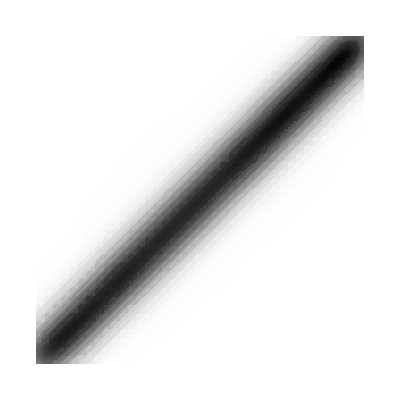

```mathematica
SmoothDensityHistogram[ssamples,"Oversmooth","PDF",ColorFunctionScaling->True,ColorFunction->(GrayLevel[1-#]&),Mesh->5,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

```mathematica
SmoothHistogram3D[ssamples,Auto,"PDF",Mesh->Auto,ColorFunction->Function[{x,y,z},GrayLevel[1-z]],MeshStyle->Auto,PlotRange->{{0,1},{0,1},{0,All}},Axes->Auto,ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
logprobi=Assuming[Element[t1,Reals]&&Element[t2,Reals],FullSimplify@Block[{r2=f+Exp@thetas},logpriorthetac[Exp@thetas]+Total@thetas]]
```

-Log[(t1^2-6 t1 Log[10]+18 Log[10]^2) (t2^2-6 t2 Log[10]+18 Log[10]^2)]+Log[Log[1000]^2/π^2]

```mathematica
mcmc=MCMC[logprobi,{{t1,0,1,Reals},{t2,0,1,Reals}},10000]
```

MCMCResult[{t1→3.323,t2→1.86007},«10000»]

```mathematica
mcmc=MCMC[logprobi,mcmc,100000]
```

MCMCResult[{t1→6.50282,t2→5.31867},«109999»]

```mathematica
{Max@#,Min@#}&@Flatten[mcmc["ParameterRun"][[10000;;]]]
```

{114.098,-87.6728}

```mathematica
mpari=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
ssamples=Cases[samplesi[[;;;;Round[Length[samplesi]/100000]]],{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[ssamples]
```

94056

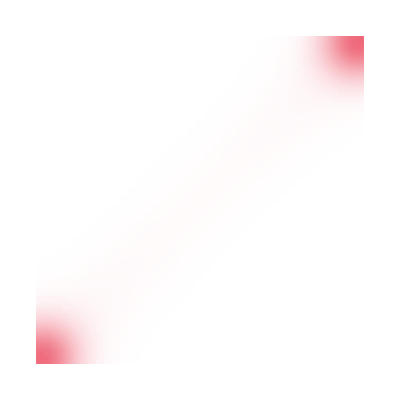

```mathematica
SmoothDensityHistogram[ssamples,"Oversmooth",ColorFunctionScaling->True,ColorFunction->mycolorfunction,Mesh->20,MeshStyle->Directive[green],PlotRange->{{0,1},{0,1}}]
```

```mathematica
logprobp=Assuming[Element[t1,Reals]&&Element[t2,Reals],FullSimplify@Block[{r2=f+Exp@thetas},
Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@Exp@thetas]-Total@LogGamma[Exp@thetas])+
logpriorthetag[Exp@thetas]+Total@thetas]]
```

(-ⅇ^t1-ⅇ^t2)/1000+t1+t2-2 Log[Gamma[ⅇ^t1] Gamma[ⅇ^t2]]+Log[Gamma[1481+ⅇ^t1] Gamma[2887+ⅇ^t1] Gamma[502+ⅇ^t2] Gamma[1159+ⅇ^t2]]+2 Log[Gamma[ⅇ^t1+ⅇ^t2]]-Log[1000 (ⅇ^t1+ⅇ^t2) Gamma[1983+ⅇ^t1+ⅇ^t2] Gamma[4046+ⅇ^t1+ⅇ^t2]]

```mathematica
mcmc=MCMC[logprobp,{{t1,0,1,Reals},{t2,0,1,Reals}},10000]
```

MCMCResult[{t1→6.079,t2→5.08718},«10000»]

```mathematica
mcmc=MCMC[logprobp,mcmc,100000]
```

MCMCResult[{t1→6.11348,t2→5.13259},«109999»]

```mathematica
{Max@#,Min@#}&@Flatten[mcmc["ParameterRun"][[10000;;]]]
```

{36.5793,-1.48314}

```mathematica
mparp=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
samplesp={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mparp;
```

```mathematica
ssamplesp=Cases[samplesp[[;;;;Round[Length[samplesp]/100000]]],{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[ssamplesp]
```

100000

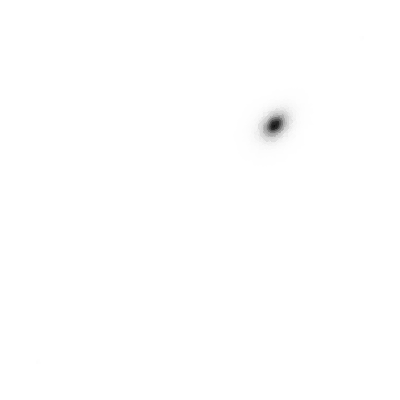

```mathematica
SmoothDensityHistogram[ssamplesp,"Oversmooth","PDF",ColorFunctionScaling->True,ColorFunction->(GrayLevel[1-#]&),Mesh->5,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

```mathematica
plotmc=SmoothHistogram3D[ssamplesp,Auto,"PDF",Mesh->Auto,ColorFunction->Function[{x,y,z},mycolorfunction[z,-1]],MeshStyle->Auto,PlotRange->{{0,1},{0,1},{0,All}},Axes->Auto,ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
SmoothHistogram3D[mparp,Auto,"PDF",Mesh->Auto,ColorFunction->Function[{x,y,z},mycolorfunction[z,-1]],MeshStyle->Auto,PlotRange->Auto,Axes->Auto,ViewPoint->Dynamic[viewpoint]]
```

```mathematica
Quantile[#,{0.05,0.95}]&/@T[mparp]
```

{{68.2909,1840.19},{25.8479,684.385}}

```mathematica
within1[x_]:=68.29090848134175<x<1840.1852094000994;
within2[x_]:=25.84793223968971<x<684.385174206752;
```

```mathematica
mpsmall=Cases[mparp,{_?within1,_?within2}];
```

```mathematica
Length[mpsmall]
```

89343

```mathematica
plotm=SmoothHistogram3D[mpsmall,Auto,"PDF",Mesh->Auto,ColorFunction->Function[{x,y,z},mycolorfunction[z,-1]],MeshStyle->Auto,PlotRange->{{0,2000},{0,2000},{0,Auto}},Axes->Auto,ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
Median[mparp]
```

{467.877,175.193}

```mathematica
Quantile[#,{0.05,0.95}]&/@T[mparp]
```

{{68.2909,1840.19},{25.8479,684.385}}

```mathematica
rmcu=Exp[Import["test_mcu_g1.csv"][[2;;,2;;]]];
```

```mathematica
Quantile[#,{0.05,0.95}]&/@T[rmcu]
```

{{64.4952,1702.17},{24.2574,638.632}}

```mathematica
within1[x_]:=68.29090848134175<x<1840.1852094000994;
within2[x_]:=25.84793223968971<x<684.385174206752;
```

```mathematica
rmcusmall=Cases[rmcu,{_?within1,_?within2}];
```

```mathematica
Length[rmcusmall]
```

90427

```mathematica
plotr=SmoothHistogram3D[rmcusmall,Auto,"PDF",Mesh->Auto,ColorFunction->Function[{x,y,z},mycolorfunction[z,1]],MeshStyle->Auto,PlotRange->{{0,2000},{0,2000},{0,Auto}},Axes->Auto,ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
ev[a_]=Mean[BetaDistribution[Hold[a[[2]]],Hold[a[[1]]]]];
va[a_]=Expectation[x^2,x\[Distributed]BetaDistribution[Hold[a[[2]]],Hold[a[[1]]]]];
```

```mathematica
statr=Import["test_mcf_g1.csv"][[2;;,2;;]];
```

```mathematica
resr=Mean[statr]
```

{0.258074,0.0000709404,0.284133,0.0000422857}

```mathematica
resm1=Mean[ReleaseHold[(ev/@T[f+#])]&/@mparp]
```

{0.259149,0.285017}

```mathematica
resm2=Mean[ReleaseHold[(va/@T[f+#])&/@mparp]]-resm1^2
```

{0.00118223,0.00108594}

```mathematica
{resr[[1]]-resr[[3]],Sqrt[resr[[2]]+resr[[4]]]}
```

{-0.0260592,0.0106408}

```mathematica
{resm1[[1]]-resm1[[2]],Sqrt[Total@resm2]}
```

{-0.0258676,0.0476253}

```mathematica
%[[1]]/%[[2]]
```

-0.543149

```mathematica
mc2ev=Mean[ReleaseHold[(ev/@T[f+#])]&/@mparc2]
```

{0.256887,0.284684}

```mathematica
mg2ev=Mean[ReleaseHold[(ev/@T[f+#])]&/@mparg2]
```

{0.259385,0.283504}

```mathematica
mcaev=Mean[ReleaseHold[(ev/@T[f+#])]&/@mparca]
```

{0.258948,0.283751}

```mathematica
Sqrt[mcvar=Mean[ReleaseHold[(va/@T[f+#])&/@mparc]]]
```

{0.00822132,0.00628716}

```mathematica
tmaxg=Exp@FindArgMax[logprobp,T[{thetas,Log[Mean@T@f]}]]
```

{724.415,270.2}

```mathematica
f+tmaxg
```

{{2205.41,3611.41},{772.2,1429.2}}

```mathematica
postf=PDF[BetaDistribution[Sequence@@(f[[;;,1]]+tmaxg)],x]*PDF[BetaDistribution[Sequence@@(f[[;;,2]]+tmaxg)],y]
```

(Piecewise[{{1.36168703232×10^741 (1-x)^771.2 x^2204.41, 0<x<1}, {0, True}}]) (Piecewise[{{2.4642764929×10^1306 (1-y)^1428.2 y^3610.41, 0<y<1}, {0, True}}])

```mathematica
plotma=Plot3D[postf,{x,0,1},{y,0,1},Mesh->Auto,ColorFunction->Function[{x,y,z},mycolorfunction[z,1]],MeshStyle->Auto,PlotRange->{{0,1},{0,1},{0,All}},Axes->Auto,ViewPoint->Dynamic[viewpoint],MeshFunctions->{#3&}]
```

-Graphics3D-

```mathematica
Show[{plotma,plotmc}]
```

-Graphics3D-

```mathematica
Max[Flatten[samplesi]]
```

Indeterminate

```mathematica
Min[Flatten[samplesi]]
```

Indeterminate

```mathematica
RandomVariate[BetaDistribution[Sequence@@a]]
```

```mathematica
BetaDistribution[Hold[a[[2]]],Hold[a[[1]]]]]
```

```mathematica
mparc2=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
logprobm=Simplify@Block[{r2=f+Exp@thetas},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@Exp@thetas]-Total@LogGamma[Exp@thetas])+logpriorthetaca[Exp@thetas]+Total@thetas]
```

t5300+t5301-2 Log[ⅇ^t5300+ⅇ^t5301]+Log[Log[1000]/(9 π Log[10]^2+π Log[ⅇ^t5300+ⅇ^t5301]^2)]-2 LogGamma[ⅇ^t5300]-2 LogGamma[ⅇ^t5301]+LogGamma[1481+ⅇ^t5300]+LogGamma[2887+ⅇ^t5300]+LogGamma[502+ⅇ^t5301]+LogGamma[1159+ⅇ^t5301]+2 LogGamma[ⅇ^t5300+ⅇ^t5301]-LogGamma[1983+ⅇ^t5300+ⅇ^t5301]-LogGamma[4046+ⅇ^t5300+ⅇ^t5301]

```mathematica
mcmc=MCMC[logprobm,{{t5300,0,1,Reals},{t5301,0,1,Reals}},10000]
```

MCMCResult[{t5300→4.18349,t5301→3.26441},«10000»]

```mathematica
mcmc=MCMC[logprobm,mcmc,100000]
```

MCMCResult[{t5300→6.22357,t5301→5.27539},«109999»]

```mathematica
mparc2=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
mparg2=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
mparca=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
Mean[mparca]
```

{5.12589×10^7,1.96058×10^7}

```mathematica
Std[mparca]
```

{3.68305×10^8,1.39321×10^8}

```mathematica
Median[mparca]
```

{176.491,65.5949}

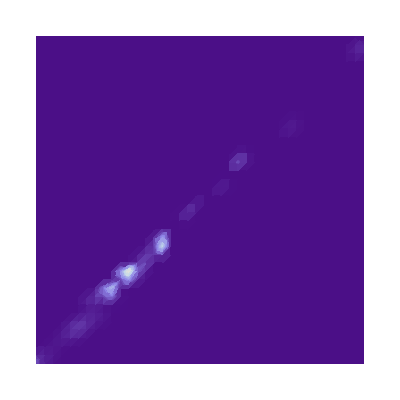

```mathematica
SmoothDensityHistogram[mparc2,"Oversmooth","PDF",ColorFunction->Auto,Mesh->5,MeshStyle->Directive[green,Dashed]]
```

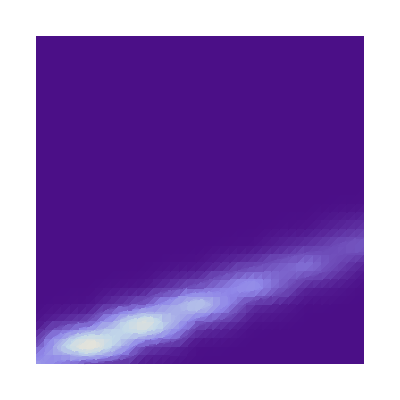

```mathematica
SmoothDensityHistogram[mparg,"Oversmooth","PDF",ColorFunction->Auto,Mesh->5,MeshStyle->Directive[green,Dashed],PlotRange->{{0,1000},{0,1000}}]
```

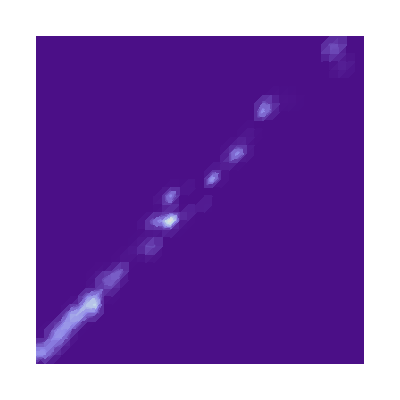

```mathematica
SmoothDensityHistogram[mparg2,"Oversmooth","PDF",ColorFunction->Auto,Mesh->5,MeshStyle->Directive[green,Dashed],PlotRange->Auto]
```

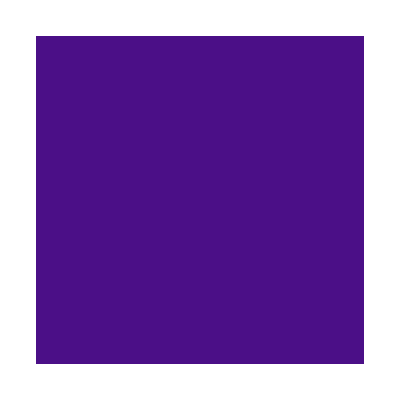

```mathematica
SmoothDensityHistogram[mparca,"Oversmooth","PDF",ColorFunction->Auto,Mesh->5,MeshStyle->Directive[green,Dashed],PlotRange->Auto]
```

```mathematica
ev[a_]=Mean[BetaDistribution[Hold[a[[2]]],Hold[a[[1]]]]];
va[a_]=Variance[BetaDistribution[Hold[a[[2]]],Hold[a[[1]]]]];
```

```mathematica
mc2ev=Mean[ReleaseHold[(ev/@T[f+#])]&/@mparc]
```

{0.258958,0.283604}

```mathematica
mc2ev=Mean[ReleaseHold[(ev/@T[f+#])]&/@mparc2]
```

{0.256887,0.284684}

```mathematica
mg2ev=Mean[ReleaseHold[(ev/@T[f+#])]&/@mparg2]
```

{0.259385,0.283504}

```mathematica
mcaev=Mean[ReleaseHold[(ev/@T[f+#])]&/@mparca]
```

{0.258948,0.283751}

```mathematica
Sqrt[mcvar=Mean[ReleaseHold[(va/@T[f+#])&/@mparc]]]
```

{0.00822132,0.00628716}

```mathematica
Sqrt[mc2var=Mean[ReleaseHold[(va/@T[f+#])&/@mparc2]]]
```

{0.00882677,0.00659103}

```mathematica
Sqrt[mg2var=Mean[ReleaseHold[(va/@T[f+#])&/@mparg2]]]
```

{0.00816641,0.00620325}

```mathematica
Sqrt[mcavar=Mean[ReleaseHold[(va/@T[f+#])&/@mparca]]]
```

{0.00832168,0.00624342}

```mathematica
Differences[mcev]/Sqrt@Total[mcvar]
```

{2.38129}

```mathematica
Differences[mc2ev]/Sqrt@Total[mc2var]
```

{2.52332}

```mathematica
Differences[mg2ev]/Sqrt@Total[mg2var]
```

{2.35188}

```mathematica
Differences[mcaev]/Sqrt@Total[mcavar]
```

{2.38417}

```mathematica
mparc2=Exp@mcmc["ParameterRun"][[10000;;]];
```

```mathematica
mgev=Mean[ReleaseHold[(ev/@T[f+#])]&/@mparg]
```

{0.257684,0.284274}

```mathematica
Sqrt[mgvar=Mean[ReleaseHold[(va/@T[f+#])&/@mparg]]]
```

{0.00852238,0.0065492}

```mathematica
Differences[mgev]/Sqrt@Total[mgvar]
```

{2.47393}

```mathematica
mgnnew=Total[mgfnew];
T[T[mgfnew]/mgnnew]//MF
```

(0.741099 | 0.71617
0.258901 | 0.28383)

```mathematica
mgsd=
```

```mathematica
logprobg[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])+logpriorthetag[t]];
logprobc[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])+logpriorthetac[t]];
logprobe[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])];
```

```mathematica
tmaxg=FindArgMax[{logprobg[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{8.49735,3.43841}

```mathematica
tmaxc=FindArgMax[{logprobc[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{0.123298,0.101888}

```mathematica
logprobm/.{thetas[[1]]->Log@tmax[[1]],thetas[[2]]->Log@tmax[[2]]}
```

-3564.

```mathematica
logprob[tmax]
```

-3559.62

```mathematica
Log@tmax
```

{-2.09315,-2.28388}

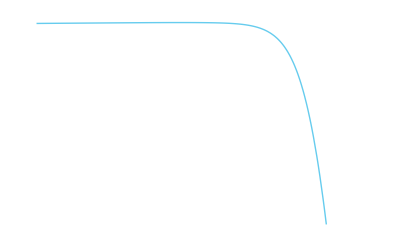

```mathematica
Plot[Evaluate[logprobm/.{thetas[[1]]->Log@tmax[[1]]}],{t5301,-10,10}]
```

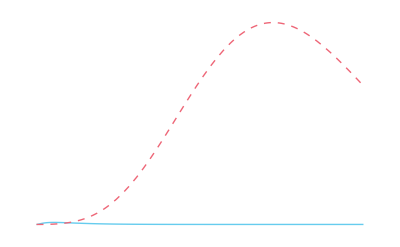

```mathematica
maxxx=Exp[logprobe[tmaxc]];Plot[{Exp[logprobe[{tmaxc[[1]],t5301}]]/maxxx,Exp[logprobe[{tmaxg[[1]],t5301}]]/maxxx},{t5301,0,5}]
```

```mathematica
Plot3D[Evaluate@Exp[logprobe[{t5300,t5301}]+{0,logpriorthetac[{t5300,t5301}],logpriorthetag[{t5300,t5301}]}]/maxxx,{t5300,0,50},{t5301,0,50},Axes->Auto,PlotRange->{0,All}]
```

```mathematica
Exp[logprob[tmax[[1]],0.12]]
```

ⅇ^logprob[0.123298,0.12]

```mathematica
(fnew=f+tmax)//MF
```

(1489.5 | 2895.5
505.438 | 1162.44)

```mathematica
mev=ev/@T[f+tmax]
```

{0.253361,0.286461}

```mathematica
msd=sd/@T[f+tmax]
```

{0.00973536,0.00709635}

```mathematica
Differences[mev]/Sqrt@Total[msd^2]
```

{2.7475}

```mathematica
nnew=Total[fnew];
T[T[fnew]/nnew]//MF
```

(0.746639 | 0.713539
0.253361 | 0.286461)

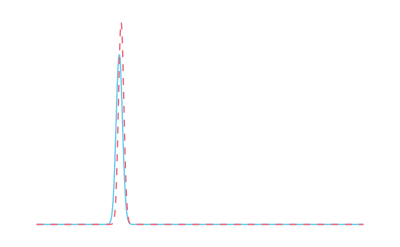

```mathematica
Plot[{bd[x,Sequence@@fnew[[;;,1]]],bd[x,Sequence@@mgfnew[[;;,1]]]},{x,0,1},PlotRange->All]
```

```mathematica
evd=ev[fnew[[;;,1]]]-ev[fnew[[;;,2]]]
```

-0.0330998

```mathematica
sdd=Sqrt[sd[fnew[[;;,1]]]^2+sd[fnew[[;;,2]]]^2]
```

0.0120472

```mathematica
evd/sdd
```

-2.7475

```mathematica
evd=ev[mgfnew[[;;,1]]]-ev[mgfnew[[;;,2]]]
```

-0.0249282

```mathematica
sdd=Sqrt[sd[mgfnew[[;;,1]]]^2+sd[mgfnew[[;;,2]]]^2]
```

0.0103988

```mathematica
evd/sdd
```

-2.39721

```mathematica
Plot[{bd[x,Sequence@@mgfnew[[;;,1]]],bd[x,Sequence@@mgfnew[[;;,2]]]},{x,0,1},PlotRange->All]
```

```mathematica
mcmc[{"BestFitParameters","ParameterErrors","AverageAcceptance","TimeSpent","NumSteps","BurnFraction","BurnEnd","CorrelationMatrix","ParameterHistograms"}]
```

```mathematica
pars=mcmc["ParameterRun"];
```

```mathematica
pars[[;;50,1]]
```

{0,0,0,0,0,0.104292,0.104292,1.44716,1.44716,1.51828,1.20462,1.20462,1.20462,1.20462,1.20462,1.20462,1.20462,1.20462,1.20462,1.20462,1.6897,1.6897,1.6897,1.6897,1.30528,1.30528,1.30528,1.30528,1.30528,2.2398,2.2398,2.05409,1.88064,1.88064,2.81164,2.81164,2.81164,2.81164,2.81164,2.81164,2.81164,2.71359,2.71359,2.71359,2.71359,2.71359,2.71359,2.71359,2.44672,2.44672}

```mathematica
Std[Exp@pars[[;;,1]]]
```

3.6156×10^8

```mathematica
Mean[Exp@pars[[;;,1]]]
```

5.61502×10^7

```mathematica
Histogram[Exp@pars[[;;,1]],100,PlotRange->{0,10^8}]
```

```mathematica
Histogram[Exp@pars[[;;,2]],"FreedmanDiaconis",PlotRange->All]
```

$Aborted

```mathematica
pars[[1]]
```

t51

```mathematica
m21=FS@Expectation[x^2,x\[Distributed]BetaDistribution[a,b]]
```

(a (1+a))/((a+b) (1+a+b))

```mathematica
FS@Expectation[(1-x)^2,x\[Distributed]BetaDistribution[a,b]]
```

(b (1+b))/((a+b) (1+a+b))

```mathematica
FS@Expectation[{x,y,z}^2,{x,y,z}\[Distributed]DirichletDistribution[{ax,ay,az,ao}]]
```

{(ax (1+ax))/((ao+ax+ay+az) (1+ao+ax+ay+az)),(ay (1+ay))/((ao+ax+ay+az) (1+ao+ax+ay+az)),(az (1+az))/((ao+ax+ay+az) (1+ao+ax+ay+az))}